```mathematica
Clear[ent,ts,α,β,s,x,y,t];
ent=0.1;
ts=1;
α=0.5;
β=2.25;
s=0.05;
S=50;

ρx=α Exp[-β s x[t]S]/ts;
ρy=α Exp[-β s y[t]S]/ts;
system={
x'[t]==-ρx x[t]+ent(1-x[t]-y[t]),
y'[t]==-ρy y[t]+ent(1-x[t]-y[t]),
y[0]==0,x[0]==0}
```

{x'[t]==-0.5 ⅇ^(-5.625 x[t]) x[t]+0.1 (1-x[t]-y[t]),y'[t]==0.1 (1-x[t]-y[t])-0.5 ⅇ^(-5.625 y[t]) y[t],y[0]==0,x[0]==0}

```mathematica
sol=NDSolve[system,{x,y},{t,0,100}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

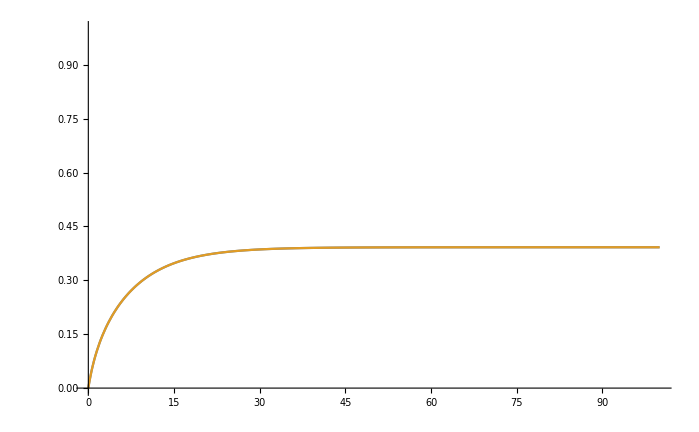

```mathematica
Plot[{x[t]/. sol,y[t]/. sol},{t,0,100},
PlotRange->{0,1}]
```

```mathematica
Clear[ent,ts,α,β,s,x,y,t];
ρx=α Exp[-β s x[t]S]/ts;
ρy=α Exp[-β s y[t]S]/ts;
system={
x'[t]==-ρx x[t]+ent(1-x[t]-y[t]),
y'[t]==-ρy y[t]+ent(1-x[t]-y[t]),
y[0]==0.05,x[0]==0.01}
```

{x'[t]==-(ⅇ^(-50 s β x[t]) α x[t])/ts+ent (1-x[t]-y[t]),y'[t]==ent (1-x[t]-y[t])-(ⅇ^(-50 s β y[t]) α y[t])/ts,y[0]==0.05,x[0]==0.01}

```mathematica
sol=NDSolve[system,{x,y},{t,0,100}]
```

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve[{x'[t]==-(ⅇ^(-50 s β x[t]) α x[t])/ts+ent (1-x[t]-y[t]),y'[t]==ent (1-x[t]-y[t])-(ⅇ^(-50 s β y[t]) α y[t])/ts,y[0]==0.05,x[0]==0.01},{x,y},{t,0,100}]

```mathematica
Manipulate[
ρx=α Exp[-β s (x[t]+ix)S]/ts;
ρy=α Exp[-β s (y[t]+iy)S]/ts;
system={
x'[t]==-ρx x[t]+ent(1-x[t]-y[t]-ix),
y'[t]==-ρy y[t]+ent(1-x[t]-y[t]-iy),
y[0]==0.0,x[0]==0.0};
sol=NDSolve[system,{x,y},{t,0,100}];
Plot[{x[t]/. sol,y[t]/. sol},{t,0,100},
PlotRange->{0,1}],
{{ts,1},0.1,5},
{{s,0.05},0.01,1},
{{S,100},10,1000},
{{ent,0.1},0.01,1},
{{β,2},0.5,5},
{{α,0.5},0,1},
{{ix,0},0,0.5},
{{iy,0},0,0.5}
]
```

```mathematica
Manipulate[
ρx=(α Exp[-β s (x[t]+ix)S])/ts;
ρy=(α Exp[-β s (y[t]+iy)S])/ts;
system={
x'[t]==-ρx x[t]+ent(1-x[t]-y[t]-iy -ix),
y'[t]==-ρy y[t]+ent(1-x[t]-y[t]-iy -ix),
y[0]==0,x[0]==0};
sol=NDSolve[system,{x,y},{t,0,18000}];
Plot[{(x[t] + ix)/. sol,(y[t]+iy)/. sol},{t,0,18000},
PlotRange->{0,1}],
{{ts,2},0.1,20},
{{s,0.25},0.01,1},
{{S,50},1,1000},
{{ent,0.001},0.01,1},
{{β,2.25},0.5,5},
{{α,0.5},0,1},
{{ix,0.3},0,0.5},
{{iy,0},0,0.5}
]
```

20 = e^(50000b)

20==ⅇ^(50000 b)

```mathematica
Solve[20==ⅇ^(50000 b),{b},Reals]
```

{{b→(2 Log[2]+Log[5])/50000}}

```mathematica
N[{{b->(2 Log[2]+Log[5])/50000}}]
```

{{b→0.0000599146}}